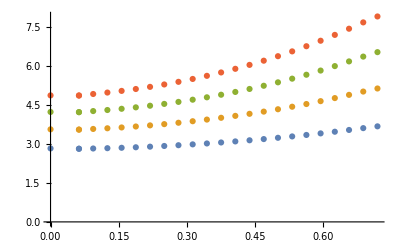

```mathematica
a={{0,2.821520},{0.062500,2.809064},{0.062500,2.809064},{0.093750,2.818764},{0.125000,2.830537},{0.156250,2.846298},{0.187500,2.865888},{0.218750,2.888998},{0.250000,2.915355},{0.281250,2.944750},{0.312500,2.977034},{0.343750,3.012116},{0.375000,3.049955},{0.406250,3.090561},{0.437500,3.133992},{0.468750,3.180352},{0.500000,3.229794},{0.531250,3.282521},{0.562500,3.338774},{0.593750,3.398805},{0.625000,3.462784},{0.656250,3.530525},{0.687500,3.600789},{0.718750,3.669519}};
a2={{0,3.554412},{0.062500,3.544038},{0.062500,3.544038},{0.093750,3.569275},{0.125000,3.595076},{0.156250,3.626382},{0.187500,3.663493},{0.218750,3.706200},{0.250000,3.754266},{0.281250,3.807514},{0.312500,3.865844},{0.343750,3.929234},{0.375000,3.997730},{0.406250,4.071446},{0.437500,4.150554},{0.468750,4.235288},{0.500000,4.325936},{0.531250,4.422834},{0.562500,4.526352},{0.593750,4.636842},{0.625000,4.754451},{0.656250,4.878483},{0.687500,5.005250},{0.718750,5.122973}};
a3={{0,4.221702},{0.062500,4.214383},{0.062500,4.214383},{0.093750,4.256033},{0.125000,4.296490},{0.156250,4.343786},{0.187500,4.398720},{0.218750,4.461221},{0.250000,4.531113},{0.281250,4.608273},{0.312500,4.692665},{0.343750,4.784343},{0.375000,4.883447},{0.406250,4.990199},{0.437500,5.104893},{0.468750,5.227889},{0.500000,5.359607},{0.531250,5.500513},{0.562500,5.651095},{0.593750,5.811792},{0.625000,5.982777},{0.656250,6.163127},{0.687500,6.347681},{0.718750,6.518592}};
a4={{0,4.857593},{0.062500,4.853503},{0.062500,4.853503},{0.093750,4.911798},{0.125000,4.967093},{0.156250,5.030530},{0.187500,5.103403},{0.218750,5.185784},{0.250000,5.277567},{0.281250,5.378690},{0.312500,5.489188},{0.343750,5.609195},{0.375000,5.738951},{0.406250,5.878787},{0.437500,6.029117},{0.468750,6.190432},{0.500000,6.363283},{0.531250,6.548265},{0.562500,6.745985},{0.593750,6.956969},{0.625000,7.181414},{0.656250,7.418258},{0.687500,7.661431},{0.718750,7.889006}};
ListPlot[{a,a2,a3,a4}]
```

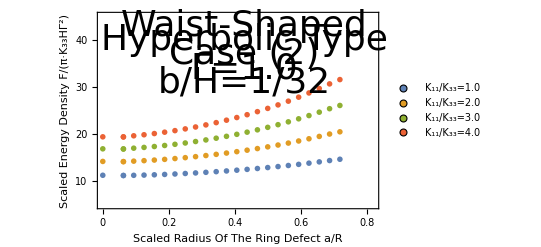

```mathematica
aa=a*Table[{1,4},{i,0,23}];
aa2=a2*Table[{1,4},{i,0,23}];
aa3=a3*Table[{1,4},{i,0,23}];
aa4=a4*Table[{1,4},{i,0,23}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{10,20,30,40},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.82},{5,45}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.43,43}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.43,40}],Text[Style["Case (2)",Directive[Black,36]],{0.43,37}],Text[Style["Γ=1.0",Directive[Black,36]],{0.43,34}],Text[Style["b/H=1/32",Directive[Black,36]],{0.43,31}]}]
```